MathematicaIO warning: redefining field speed, but memory is not freed until library is unloaded.
Field verbosity defaults to 1
Field origin defaults to {0,0}
Field sndOrder defaults to 0
Fast marching solver completed in 0.000298 s.
Field exportActiveNeighs defaults to 0
Field exportGeodesicFlow defaults to 0
Unused fields : FMCPUTime MaxStencilWidth StencilCPUTime nAccepted

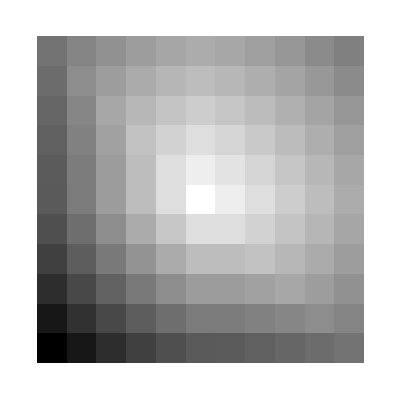

```mathematica
Module[{params=Association[{}],n=11,values,test,used,defaulted},
params["model"]="IsotropicBox2<Boundary::Closed>";
params["speed"]=Array[1.&,{n,n}];
params["dims"]={n,n};
params["gridScale"]=1./n;
params["seeds"]={{0.5,0.5}};
params["exportValues"]=1.;

LoadHFMWLL[hfmLibraryPath];
hfmSetVariable[#1,#2]&@@@Normal[params];
hfmSetVariable["speed",Array[If[#1>#2,1.,2.]&,{n,n}]];
hfmRunModel[];
values=hfmGetArray[2]["values"];
UnloadHFMWLL[];
ArrayPlot[values]
]
```

```mathematica
Print["Hi"];Print["There"];
```

Hi

There